```mathematica
<<RLBot`;
```

```mathematica
data = ImportNDJSON["backboard.ndjson", {2}][[1;;500]];
```

```mathematica
x = #["car"]["x"] & /@ data;
v = #["car"]["v"] & /@ data;
wLocal = (#["car"]["w"].#["car"]["o"]) & /@ data;
o = #["car"]["o"] & /@ data;
s = #["s"] & /@ data;
times = (#["time"]-data[[1]]["time"]) & /@ data;

Graphics3D[{
Line[x]
}]
```

-Graphics3D-

```mathematica
path = data[[1]]["path"];
follow = data[[1]]["follow"];
timePlan = #[[1]] & /@ follow["plan"][[1]];
speedPlan = #[[2, 2]] & /@ follow["plan"][[1]];
distancePlan = #[[2, 1]] & /@ follow["plan"][[1]];
```

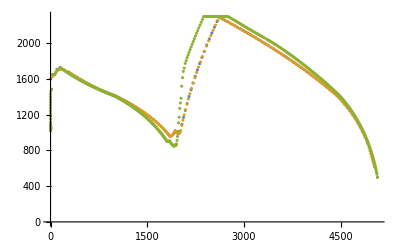

```mathematica
ListPlot[{
Transpose[{path["distances"], path["max_speeds"]}],
Transpose[{distancePlan, speedPlan}],
Transpose[{s,Norm /@ v}]
}]
```

```mathematica
ListPlot[{
Transpose[{timePlan, distancePlan}],
Transpose[{times, s}]
}]
```

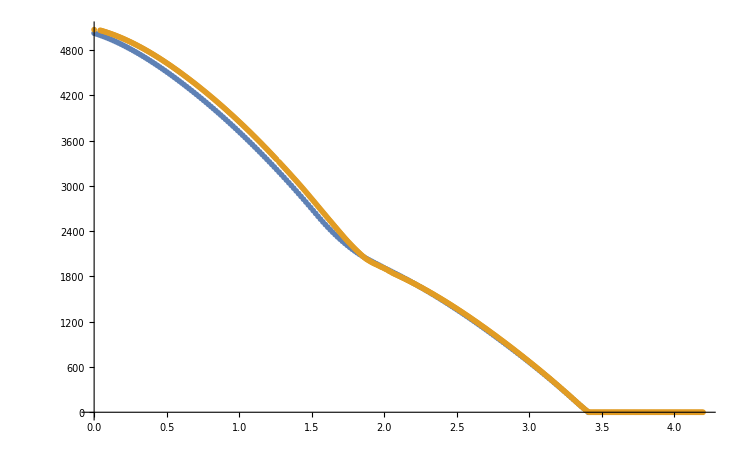

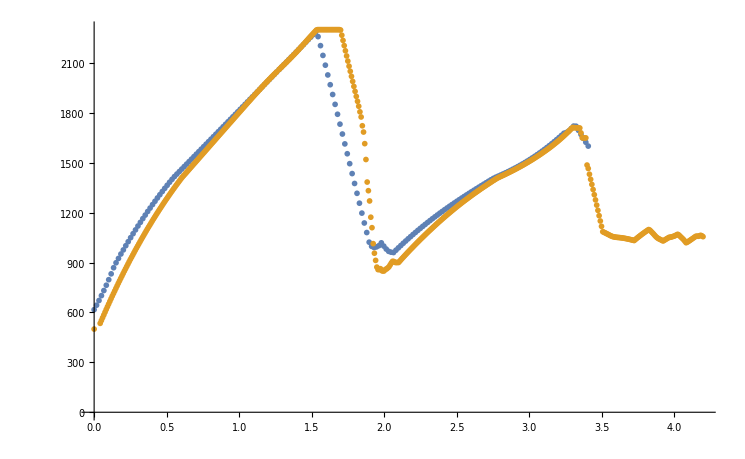

```mathematica
ListPlot[{
Transpose[{Reverse[timePlan], distancePlan}],
Transpose[{times, s}]
}]

ListPlot[{
Transpose[{Reverse[timePlan], speedPlan}],
Transpose[{times, Norm /@ v}]
}]
```

```mathematica
FullSimplify[InterpolatingPolynomial[{{0, v0, 0}, {T, 0, 0}}, t] /. t-> τ T]
FullSimplify[InterpolatingPolynomial[{{0, 0, 0}, {T, vT, 0}}, t]/. t-> τ T]
FullSimplify[InterpolatingPolynomial[{{0, 0, 0}, {T, 0, aT}}, t]/. t-> τ T]
```

v0 (-1+τ)^2 (1+2 τ)

vT (3-2 τ) τ^2

aT T (-1+τ) τ^2